Приближенное решение данной задачи Коши имеет вид: 1/945 x (945+315 x^2+63 x^4+9 x^6+x^8)-(x (189-210000 x^2+20000000 x^4) Cos[100 x])/200000000000000000+(3 (63-280000 x^2+100000000 x^4) Sin[100 x])/20000000000000000000

Точное решение данной задачи Коши имеет вид: ⅇ^(x^2/2) √(π/2) Erf[x/(√2)]

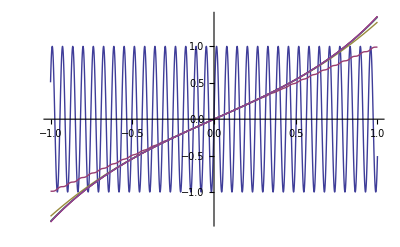

Погрешность приближения равна: 0.0000171556

```mathematica
(*Зададим правую часть дифференциального уравнения*)
f[x_,y_]=x*y+1;
(*Зададим начальные условия*)
x0=0;
y0=0;
(*Зададим количество итераций*)
n=5;
(*Зададим начальное приближение*)
Y={Sin[100*x]};
(*Построим последовательность итераций метода Пикара*)
For[k=1,k≤n,k++,
AppendTo[Y,y0+Integrate[f[x,Y[[k]]],{x,x0,x}]]
];
(*Найдем точное решение данной задачи Коши*)
Sol=DSolve[{g'[x]==f[x,g[x]],g[x0]==y0},g[x],x];
sol[x_]=g[x]/.Sol[[1]];
Print["Приближенное решение данной задачи Коши имеет вид: ",Y[[n+1]]]
Print["Точное решение данной задачи Коши имеет вид: ",sol[x]]
(*Построим графики точного решения и последовательности итераций в окрестности точки x0 в одной системе координат*)
G=Plot[sol[x],{x,x0-1,x0+1},PlotStyle->Red];
GIt=Plot[Y,{x,x0-1,x0+1}];
Show[G,GIt]
(*Найдем погрешность вычислений*)
r=NIntegrate[Abs[sol[x]-Y[[n+1]]],{x,x0-1,x0+1}];
Print["Погрешность приближения равна: ",r]
(*Выполним анимацию приближений к решению задачи Коши*)
Animate[Show[G,Plot[Y[[k]],{x,x0-1,x0+1}]],{k,1,n+1,1},AnimationRunning->False]
```